{lambda→100.}

100.

The value of lambda that gives a mean of 0.01 is: 100.

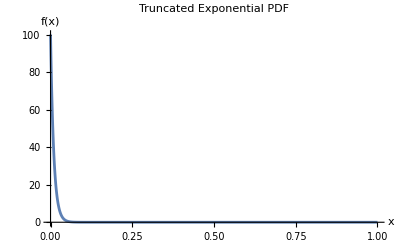

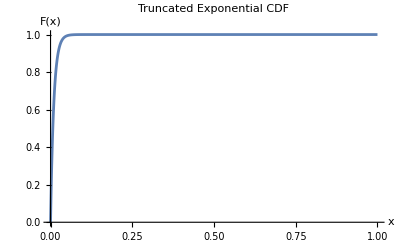

0.01

The calculated mean is: 0.01

```mathematica
(*Define the correct equation for the mean*)equation[lambda_]:=1/lambda-Exp[-lambda]/(1-Exp[-lambda])-0.01

(*Solve the equation numerically*)
solution=FindRoot[equation[lambda]==0,{lambda,1}]

(*Extract the value of lambda*)
lambdaValue=lambda/. solution

(*Print the result*)
Print["The value of lambda that gives a mean of 0.01 is: ",lambdaValue]

(*Define the truncated PDF*)
truncatedPDF[x_]:=(lambdaValue*Exp[-lambdaValue*x])/(1-Exp[-lambdaValue])

(*Define the truncated CDF*)
truncatedCDF[x_]:=(1-Exp[-lambdaValue*x])/(1-Exp[-lambdaValue])

(*Plot the PDF*)
Plot[truncatedPDF[x],{x,0,1},PlotLabel->"Truncated Exponential PDF",AxesLabel->{"x","f(x)"},PlotRange->All]

(*Plot the CDF*)
Plot[truncatedCDF[x],{x,0,1},PlotLabel->"Truncated Exponential CDF",AxesLabel->{"x","F(x)"},PlotRange->All]

(*Verify the mean*)
mean=NIntegrate[x*truncatedPDF[x],{x,0,1}]
Print["The calculated mean is: ",mean]
```

```mathematica
x[y_]:=-1/100 Log[1-y+y Exp[-100]]
```

```mathematica
x[Random[]]
```

0.0150789

```mathematica
Commonest[Table[x[Random[]] , {i,1,100}]]
```

{0.00324366,0.010769,0.00846418,0.000628135,0.0116379,0.00769528,0.0338174,0.0433002,0.0046478,0.0129575,0.0207547,0.0054984,0.00140736,0.00221003,0.00490803,0.0154312,0.0462222,0.00304408,0.00732692,0.00991237,0.00185767,0.011535,0.0261317,0.00866848,0.0223044,0.000254403,0.00439508,0.00731565,0.00229186,0.00670117,0.00493698,0.00759312,0.0179032,0.0143567,0.0072388,0.00115471,0.0121003,0.0082956,0.00136126,0.00389741,0.0124355,0.00358561,0.0093619,0.0118379,0.00781124,0.00959325,0.0114314,0.00121218,0.0104865,0.00895825,0.00393837,0.00904645,0.00588375,0.00109121,0.0274733,0.000653954,0.00945921,0.00417538,0.00546053,0.0308454,0.0240647,0.0150316,0.00347433,0.00998264,0.00220927,0.00646753,0.0115715,0.0277413,0.0106745,0.0196189,0.0000444703,0.0173408,0.0000654684,0.00311535,0.0113601,0.00258929,0.00824976,0.00179486,0.0135868,0.00180107,0.0299726,0.0173142,0.00388949,0.00236445,0.000410402,0.000464543,0.000291509,0.00865335,0.0184506,0.00841962,0.00420239,0.0102581,0.00205634,0.0123694,0.00413507,0.0170406,0.00197651,0.00583486,0.0107814,0.00891435}

```mathematica
Sum[Table[x[Random[]] , {i,1,100}][[i]],{i,1,100}]/100
```

0.00887658

```mathematica
x[0.6904392304356651]
```

0.011726

```mathematica
x[0.985267027338285]
```

0.0421767